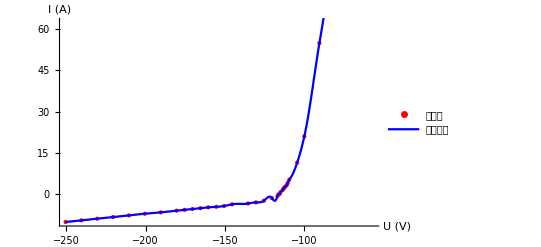

```mathematica
(*定义数据数组*)U=-1*{250.4,240.5,230.5,220.5,210.5,200.5,190.5,180.5,175.5,170.5,165.5,160.5,155.5,150.5,145.5,135.5,130.5,125.5,120.5,116.9,116.3,115.5,115.0,113.6,113.0,112.5,112.0,111.0,110.5,109.5,104.5,100.0,90.5,80.5,70.0,65.0,60.5,57.0};
I0={-10.0,-9.4,-8.8,-8.2,-7.6,-7.0,-6.5,-5.9,-5.6,-5.3,-5.0,-4.7,-4.5,-4.2,-3.6,-3.3,-2.9,-2.3,-1.3,-0.6,0,0.2,0.8,1.6,2.2,2.5,2.8,3.4,4.1,5.3,11.5,21.0,54.8,132.4,476.7,838.6,1435.8,1978.2};

(*绘制 I-U 散点图*)
scatterPlot=ListPlot[Transpose[{U,I0}],PlotStyle->{Red,PointSize[Large]},AxesLabel->{"U (V)","I (A)"},PlotLegends->{"数据点"}];

(*样条拟合*)
splineFit=Interpolation[Transpose[{U,I0}],Method->"Spline"];

(*绘制 I-U 样条拟合曲线*)
splinePlot=Plot[splineFit[x],{x,Min[U],Max[U]},PlotStyle->Blue,PlotLabel->"I-U 样条拟合曲线",PlotLegends->{"拟合曲线"}];

(*显示散点图和拟合曲线*)
plot=Show[scatterPlot,splinePlot];

(*显示图像*)
plot
```

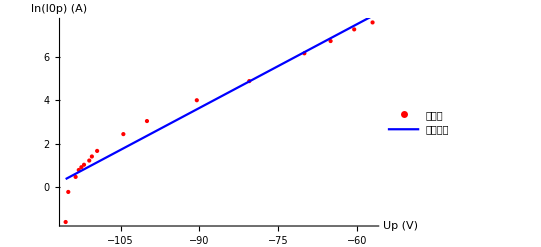

拟合方程: 15.2188+0.128557 x

相关系数 (R.b2): 0.947773

拟合参数：

| Estimate | Standard Error | t-Statistic | P-Value
1 | 15.2188 | 0.743312 | 20.4743 | 2.24602×10^-12
x | 0.128557 | 0.00753154 | 17.0692 | 3.09195×10^-11

斜率: 0.128557

截距: 15.2188

标准误差: 0.411726

```mathematica
(*定义数据数组*)Up0=-1*{115.5,115.0,113.6,113.0,112.5,112.0,111.0,110.5,109.5,104.5,100.0,90.5,80.5,70.0,65.0,60.5,57.0};
I0p={0.2,0.8,1.6,2.2,2.5,2.8,3.4,4.1,5.3,11.5,21.0,54.8,132.4,476.7,838.6,1435.8,1978.2};

(*对 I0p 取自然对数*)
lnI0p=Log[I0p];

(*绘制 Up0 与 lnI0p 的散点图*)
scatterPlot=ListPlot[Transpose[{Up0,lnI0p}],PlotStyle->{Red,PointSize[Large]},AxesLabel->{"Up (V)","ln(I0p) (A)"},PlotLegends->{"数据点"}];

(*线性回归拟合*)
fit=LinearModelFit[Transpose[{Up0,lnI0p}],x,x];

(*获取拟合方程和参数*)
fitFunction=fit["BestFit"];
slope=fit["BestFitParameters"][[2]];
intercept=fit["BestFitParameters"][[1]];

(*获取相关系数*)
r=fit["AdjustedRSquared"];
stdError=fit["EstimatedVariance"];

(*绘制拟合直线*)
fitPlot=Plot[fitFunction,{x,Min[Up0],Max[Up0]},PlotStyle->Blue,PlotLabel->"线性拟合曲线",PlotLegends->{"拟合曲线"}];

(*显示散点图和拟合曲线*)
Show[scatterPlot,fitPlot]

(*输出结果*)
Print["拟合方程: ",fitFunction]
Print["相关系数 (R.b2): ",r]
Print["拟合参数："]
Print[fit["ParameterTable"]]
Print["斜率: ",slope]
Print["截距: ",intercept]
Print["标准误差: ",stdError]
```

```mathematica
Te=5040/0.1285571495272443
```

39204.4